```mathematica
NotebookEvaluate["definitions.nb"]
```

## Phase diagram

Batch command and job timings in seconds (artemis 3x faster than headnode per core):

python ratemodel_20211202.py submit_reps 1000 0.001 100000 100 0.25 100 200 5 5 300 5 50

find ratemodel_20211202_run_subjob_1000_0.001_100000_100_0.25/job/ -name *OU | xargs -n1 -P0 tail -1 | cut -f1 -d' ' | python -c 'print("py"); import sys, numpy as np; vals = [float(x) for x in sys.stdin.readlines()]; print(np.mean(vals), np.std(vals), np.min(vals), np.max(vals), len(vals))'
py
227.48074789014316 77.16349008452744 34.997806787490845 475.4136338233948 63000

```mathematica
Run[StringTemplate["rsync mwar3732@hpc.sydney.edu.au:/project/THAP/mwar3732/`` /import/orr1/wardak/artemis -av --exclude='job/*'"]["ratemodel_20211202_run_subjob_1000_0.001_100000_100_0.25"]]
```

0

```mathematica
(relaxationTimesArtemis=Apply[Join,ParallelTable[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"]["ratemodel_20211202_run_subjob_1000_0.001_100000_100_0.25",alpha100,g100,rep],"Real32"],{}],{alpha100,100,200,5},{g100,5,300,5},{rep,0,49}],{2}])//ByteCount[#]/2.^20&
```

480.829

```mathematica
PrintTemporary@Dynamic@{alpha100,g100,rep};(relaxationTimesHeadnode=Apply[Join,ParallelTable[Quiet@Check[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/``/alpha_``_g_``_rep_``.dat"]["ratemodel_20211202_run_subjob_1000_0.001_100000_100_0.25",alpha100,g100,rep],"Real32"],{}],{alpha100,100,200,5},{g100,5,300,5},{rep,0,49}],{2}])//ByteCount[#]/2.^20&
```

480.837

```mathematica
(relaxationTimes=MapThread[Join,{relaxationTimesHeadnode,relaxationTimesArtemis},2])//ByteCount[#]/2.^20&
```

961.481

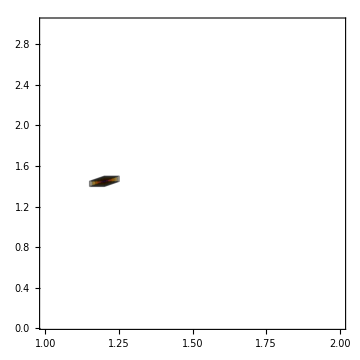

```mathematica
relaxationTimes//Transpose//Map[Length,#,{2}]&//ListContourPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors",ImageSize->Medium]&
```

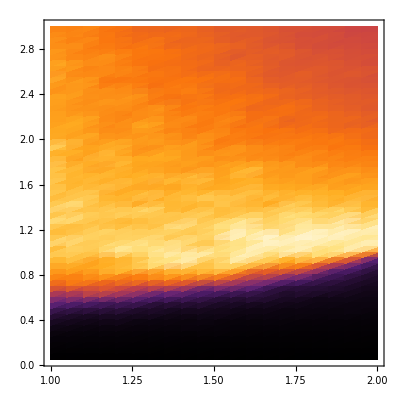
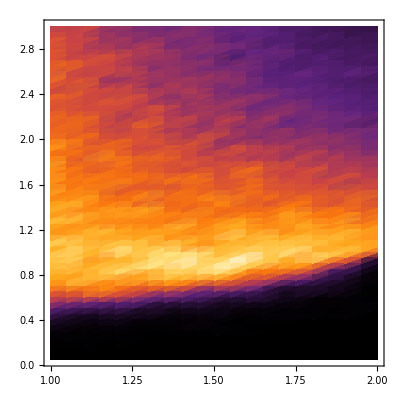
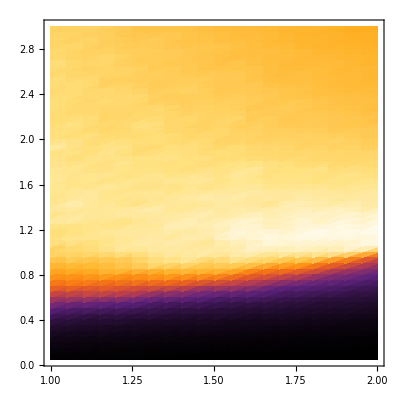
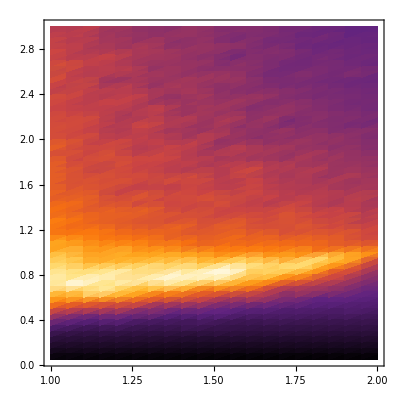
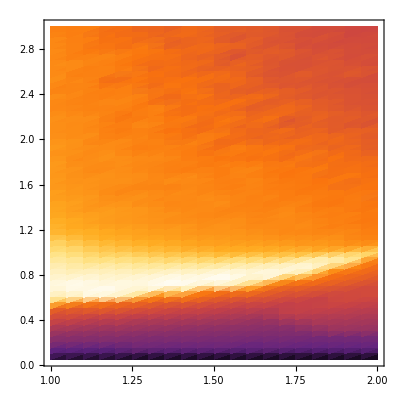
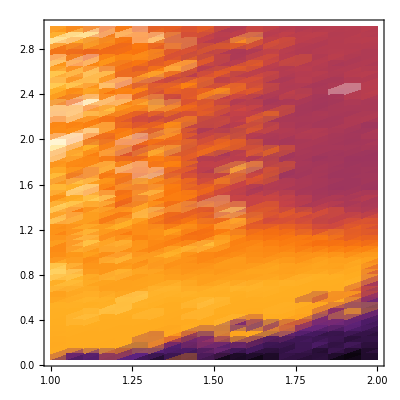

```mathematica
relaxationTimes//{Map[Mean,#,{2}],Map[Variance,#,{2}],Map[Mean,Log@#,{2}],Map[Variance,Log@#,{2}],Map[Subtract@@Quantile[#,{.95,.05}]&,Log@#,{2}],Map[Apply[Subtract]@*Reverse@*MinMax,Log@#,{2}](*,relaxationTimesOutlierCount*)}&//Map[ListDensityPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors"]&@*Transpose]
```

```mathematica
(relaxationTimesLong=Apply[Join,ParallelTable[Quiet@Check[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/``/alpha_``_g_``_rep_``.dat"]["ratemodel_20220420_run_subjob_1000_0.1_100000_10_0.25",alpha100,g100,rep],"Real32"],{}],{alpha100,100,200,5},{g100,5,300,5},{rep,0,49}],{2}])//ByteCount[#]/2.^20&
```

480.837

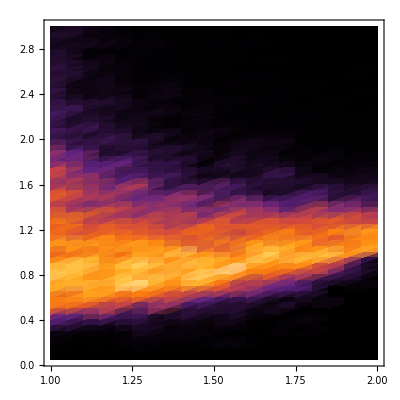
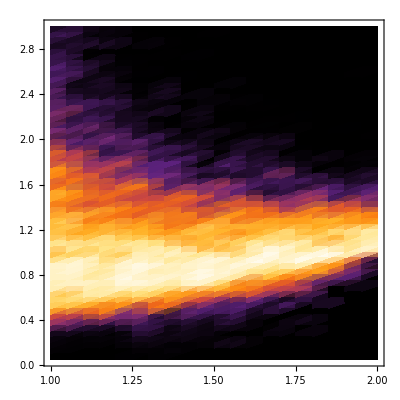
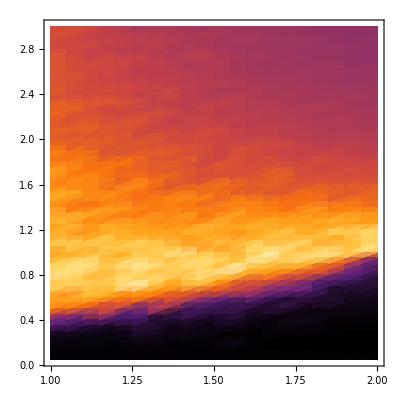
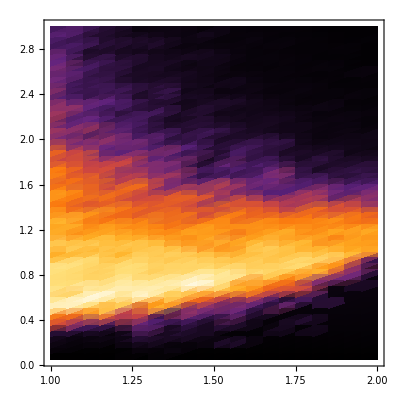
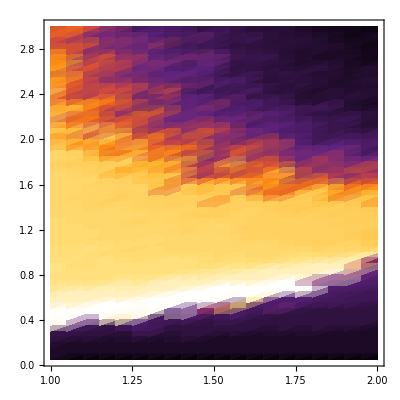
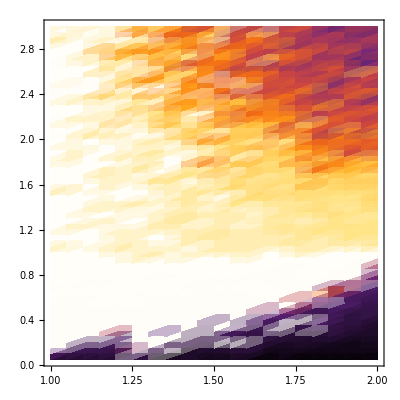

```mathematica
relaxationTimesLong//{Map[Mean,#,{2}],Map[Variance,#,{2}],Map[Mean,Log@#,{2}],Map[Variance,Log@#,{2}],Map[Subtract@@Quantile[#,{.95,.05}]&,Log@#,{2}],Map[Apply[Subtract]@*Reverse@*MinMax,Log@#,{2}](*,relaxationTimesOutlierCount*)}&//Map[ListDensityPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors"]&@*Transpose]
```

```mathematica
(relaxationTimesLongStructured=ParallelTable[Quiet@Check[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/``/alpha_``_g_``_rep_``.dat"]["ratemodel_20220420_run_subjob_1000_0.01_100000_10_0.25",alpha100,g100,rep],"Real32"],{}],{alpha100,100,200,5},{g100,5,300,5},{rep,0,49}])//ByteCount[#]/2.^20&
```

499.467

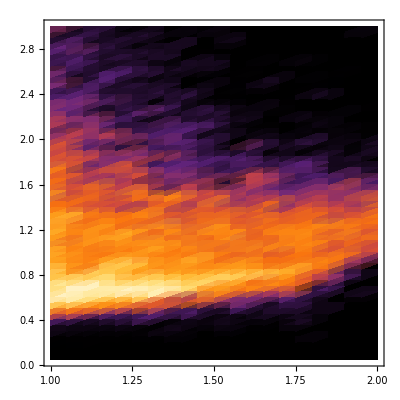
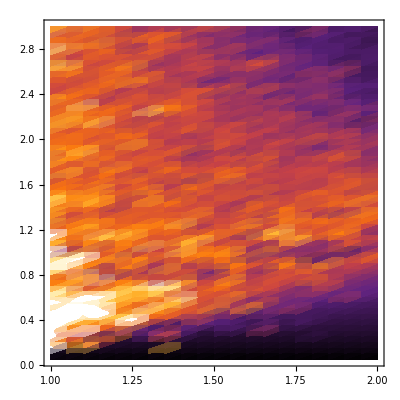
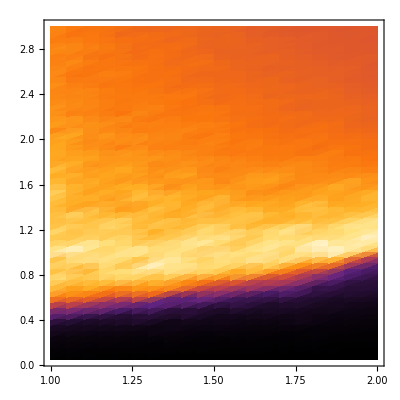
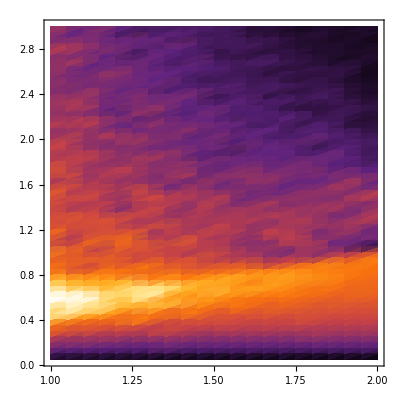
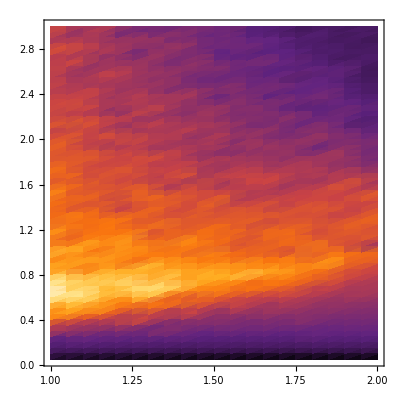
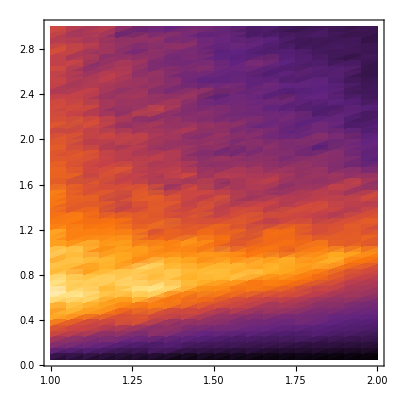

```mathematica
relaxationTimesLongStructured//{Map[Variance,#,{3}]//Map[Variance,#,{2}]&,Map[Variance[#]/Mean[#]^2&,#,{3}]//Map[Mean,#,{2}]&,Map[Mean,Log@#,{3}]//Map[Mean,#,{2}]&,Map[StandardDeviation[#]/Mean[#]&,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Subtract@@Quantile[#,{.95,.05}]&,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Apply[Subtract]@*Reverse@*MinMax,Log@#,{3}]//Map[Mean,#,{2}]&(*,relaxationTimesOutlierCount*)}&//Map[ListDensityPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors"]&@*Transpose]
```

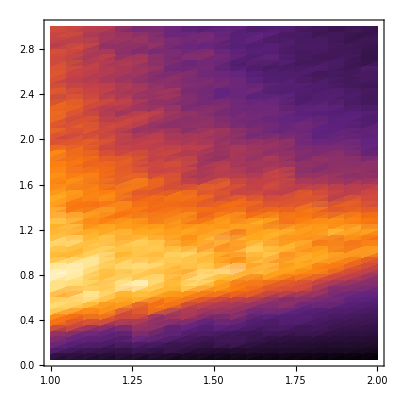

n = 2000

python ratemodel_20220408_gpu.py submit_reps 2000 0.001 100000 100 0.25 100 200 5 5 300 5 100 defaultQ 4GB

find ratemodel_20220408_gpu_run_subjob_2000_0.001_100000_100_0.25/job/ -name *OU | xargs -n1 grep elapsed | cut -f1 -d' ' | python -c 'import sys, numpy as np; vals = [float(x) for x in sys.stdin.readlines()]; print(np.mean(vals), np.std(vals), np.min(vals), np.max(vals), len(vals))'
8.49753834778922 0.5236981925015626 6.75096321105957 55.84031105041504 126000

```mathematica
Run[StringTemplate["rsync mwar3732@hpc.sydney.edu.au:/project/THAP/mwar3732/`` /import/orr1/wardak/artemis -av --exclude='job/*'"]["ratemodel_20220408_gpu_run_subjob_2000_0.001_100000_100_0.25"]]
```

0

```mathematica
(relaxationTimes2000=Apply[Join,ParallelTable[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"]["ratemodel_20220408_gpu_run_subjob_2000_0.001_100000_100_0.25",alpha100,g100,rep],"Real32"],{}],{alpha100,100,200,5},{g100,5,300,5},{rep,0,99}],{2}])//ByteCount[#]/2.^20&
```

1922.79

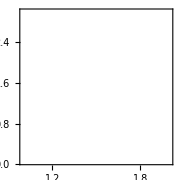

```mathematica
relaxationTimes2000//Transpose//Map[Length,#,{2}]&//ListContourPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors",ImageSize->Small]&
```

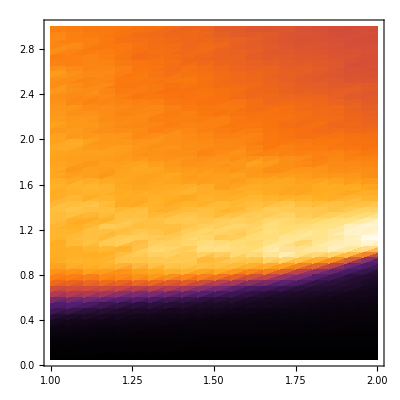
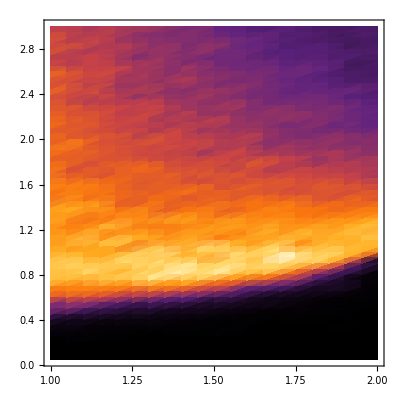
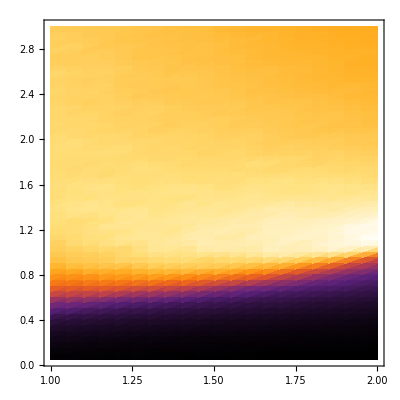
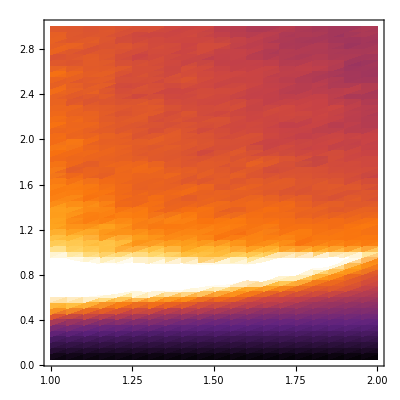
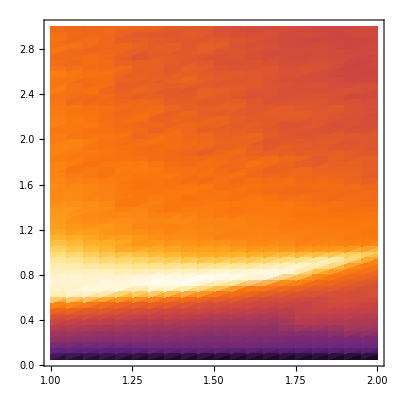
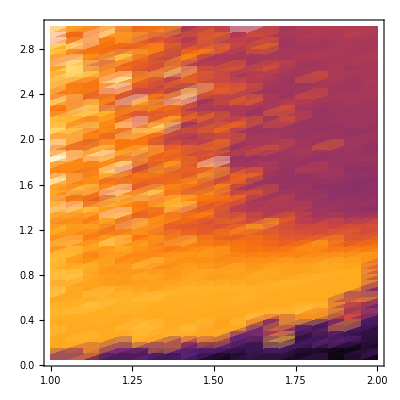

```mathematica
relaxationTimes2000//{Map[Mean,#,{2}],Map[Variance,#,{2}],Map[Mean,Log@#,{2}],Map[Variance,Log@#,{2}],Map[Subtract@@Quantile[#,{.95,.05}]&,Log@#,{2}],Map[Apply[Subtract]@*Reverse@*MinMax,Log@#,{2}](*,relaxationTimesOutlierCount*)}&//Map[ListDensityPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors"]&@*Transpose]
```

```mathematica
(relaxationTimes2000Structured=ParallelTable[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"]["ratemodel_20220408_gpu_run_subjob_2000_0.001_100000_100_0.25",alpha100,g100,rep],"Real32"],{}],{alpha100,100,200,5},{g100,5,300,5},{rep,0,99}])//ByteCount[#]/2.^20&
```

1983.3

```mathematica
relaxationTimes2000Structured//Dimensions
```

{21,60,100,2000}

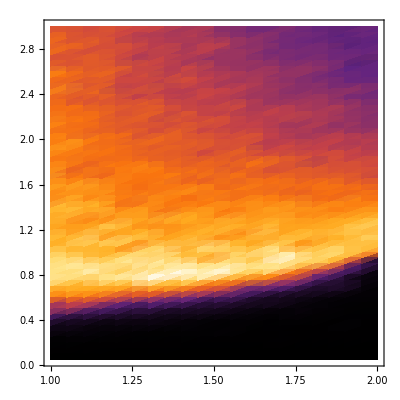
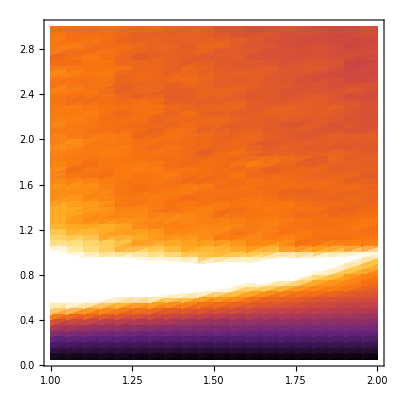
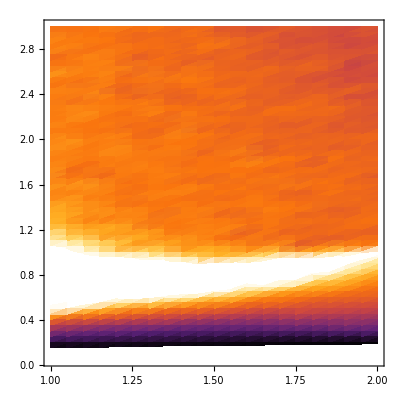
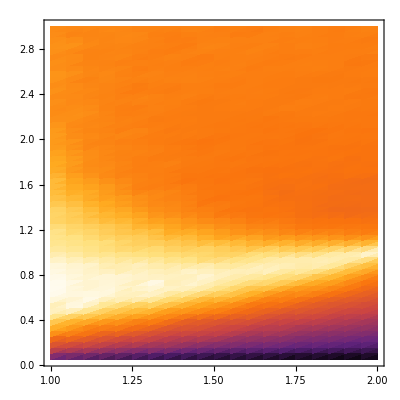
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
relaxationTimes2000Structured//{Map[Mean,#,{3}]//Map[Mean,#,{2}]&,Map[Variance,#,{3}]//Map[Mean,#,{2}]&,Map[Mean,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Variance,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Subtract@@Quantile[#,{.95,.05}]&,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Apply[Subtract]@*Reverse@*MinMax,Log@#,{3}]//Map[Mean,#,{2}]&(*,relaxationTimesOutlierCount*)}&//Map[ListDensityPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors"]&@*Transpose]
```

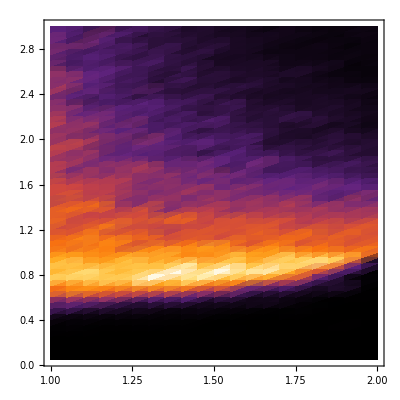
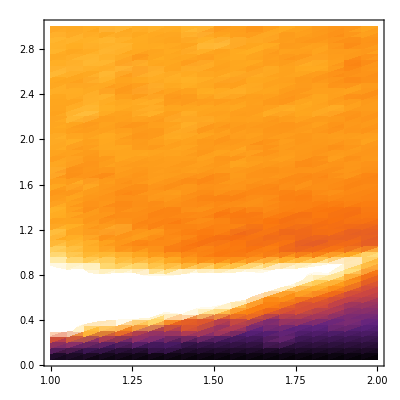
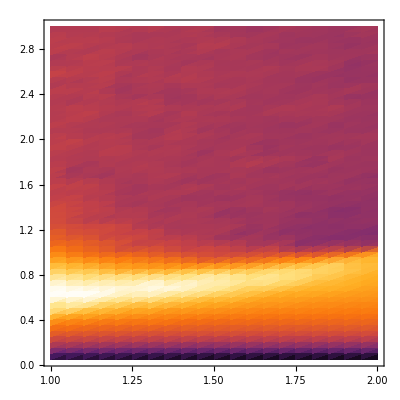
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
relaxationTimes2000Structured//{Map[Variance,#,{3}]//Map[Variance,#,{2}]&,Map[Variance[#]/Mean[#]^2&,#,{3}]//Map[Mean,#,{2}]&,Map[Mean,Log@#,{3}]//Map[Mean,#,{2}]&,Map[StandardDeviation[#]/Mean[#]&,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Subtract@@Quantile[#,{.95,.05}]&,Log@#,{3}]//Map[Mean,#,{2}]&,Map[Apply[Subtract]@*Reverse@*MinMax,Log@#,{3}]//Map[Mean,#,{2}]&(*,relaxationTimesOutlierCount*)}&//Map[ListDensityPlot[#,DataRange->{{1,2},{.05,3}},ColorFunction->"SunsetColors"]&@*Transpose]
```

## Relaxation time distribution

Batch command:

python ratemodel_20211202.py submit_reps 1000 0.1 1000000 10 0.25 120 200 80 75 300 75 1000

find ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25/job/ -name *OU | xargs -n1 grep elapsed | tqdm | cut -f1 -d' ' | python -c 'import sys, numpy as np; vals = [float(x) for x in sys.stdin.readlines()]; print(np.mean(vals), np.std(vals), np.min(vals), np.max(vals), len(vals))'
8397it [00:11, 733.78it/s]
1945.6250670520099 3796.2210731908513 265.6247992515564 13441.896100521088 8397

```mathematica
Run[StringTemplate["rsync mwar3732@hpc.sydney.edu.au:/project/THAP/mwar3732/`` /import/orr1/wardak/artemis -av --exclude='job/*'"]["ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"]]
```

0

```mathematica
PlotDistWithLogLogInset[data__]:=With[{xlim=20,label={ShiftFrameLabel[15]@"Relaxation time",ShiftFrameLabel[-5]@"Density"},imageSize=Small,ticksSize=Medium,plotStyle=ColorData[108]},ListLinePlot[HistogramPDFList[#,{Range[xlim+1]}]&/@{data},PlotMarkers->{Automatic,Tiny},PlotRange->{{0,xlim},{0,.5}}(*PlotTheme->"Scientific"*),ImageSize->imageSize,Frame->{True,True,False,False},FrameLabel->label,Evaluate@FigureStyle@pubStyle[ticksSize],PlotStyle->plotStyle,ImagePadding->{{50,10},{50,10}},PlotRangeClipping->False]~Show~Graphics@Inset[ListLogLogPlot[HistogramPDFList[#,{"Log",{.5}}]&/@{data},PlotRange->{{1,100000},{1*^-10,10}},Joined->True(*PlotTheme->"Scientific"*),PlotMarkers->{Automatic,Tiny},FrameTicks->{Table[{10^n,StringForm["10^(``)",n]},{n,1,5,2}],Table[{10^n,StringForm["10^(``)",n]},{n,-9,-1,4}]},Frame->{True,True,False,False},Evaluate@FigureStyle@pubStyle[ticksSize],PlotStyle->plotStyle]~Show~ListLogLogPlot[{{1,1},{1*^6,1*^-12}},Joined->True,PlotStyle->{Black,Dashed}],Scaled@{1,1},Scaled@{1,1},Scaled@.9]]
```

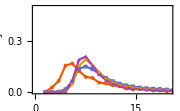

```mathematica
PrintTemporary@Dynamic@{g100,rep};With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},Apply[Join,Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,120,g100,rep],"Real32"],{}],{g100,75,300,75},{rep,0,999}],{1}]/(1*1)//PlotDistWithLogLogInset[Sequence@@#]&]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

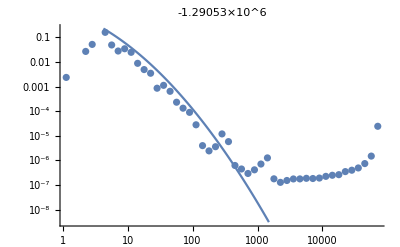
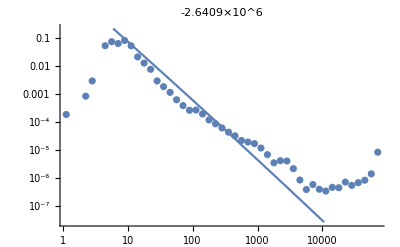
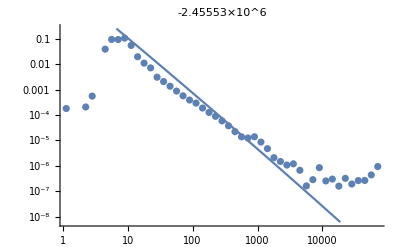
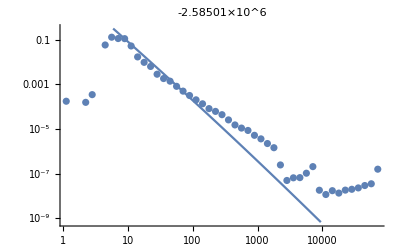
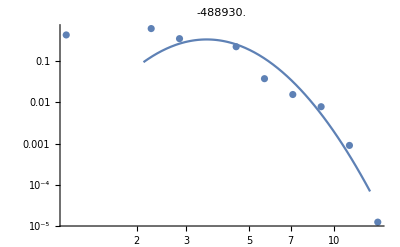
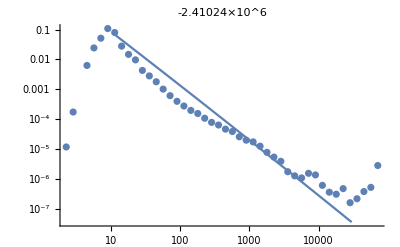
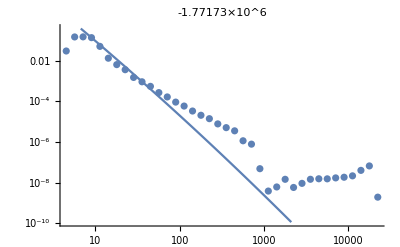
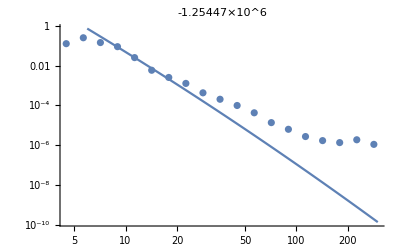

```mathematica
BlockParallel[5,ParallelOuter[{alpha100,g100}↦With[{data=With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},Join@@Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"],{}],{rep,0,999}]]},With[{dataRange=Table[#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],{f,{Max,Min@*Select[Positive]}}]&@HistogramPDFList[data,{"Log",{.05}}]},With[{estDist=EstimatedDistribution[Select[data,Between[dataRange]],TruncatedDistribution[dataRange,LogNormalDistribution[α,β]]]},ListLogLogPlot[HistogramPDFList[data,{"Log",{.1}}],PlotLabel->LogLikelihood[estDist,Select[data,Between[dataRange]]]]~(Show[##,PlotRange->All]&)~Plot[PDF[estDist,x],{x,Sequence@@dataRange},ScalingFunctions->{"Log","Log"}]]]],{120,200},Range[75,300,75]]]
```

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Grid//Export["fig/relaxationtime_fit_lognormal_1000.pdf",#]&
```

fig/relaxationtime_fit_lognormal_1000.pdf

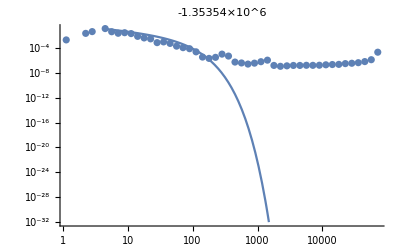
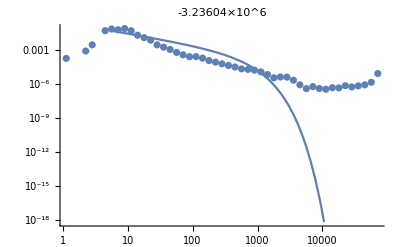
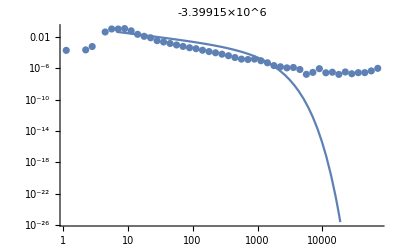
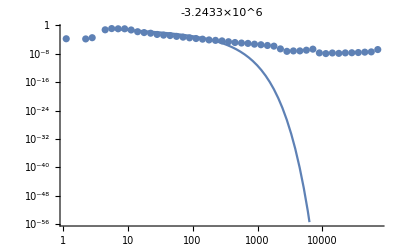
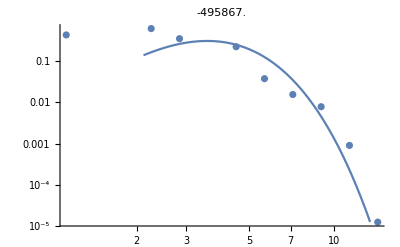
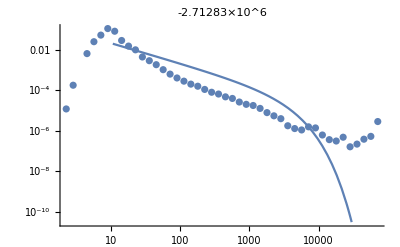
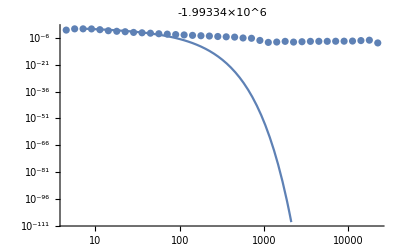
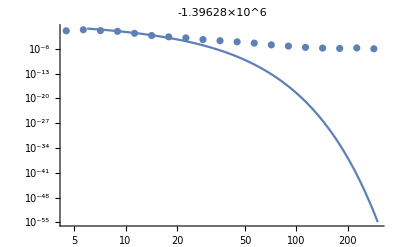

```mathematica
BlockParallel[5,ParallelOuter[{alpha100,g100}↦With[{data=With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},Join@@Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"],{}],{rep,0,999}]]},With[{dataRange=Table[#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],{f,{Max,Min@*Select[Positive]}}]&@HistogramPDFList[data,{"Log",{.05}}]},With[{estDist=EstimatedDistribution[Select[data,Between[dataRange]],TruncatedDistribution[dataRange,GammaDistribution[α,β]]]},ListLogLogPlot[HistogramPDFList[data,{"Log",{.1}}],PlotLabel->LogLikelihood[estDist,Select[data,Between[dataRange]]]]~(Show[##,PlotRange->All]&)~Plot[PDF[estDist,x],{x,Sequence@@dataRange},ScalingFunctions->{"Log","Log"}]]]],{120,200},Range[75,300,75]]]
```

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Grid//Export["fig/relaxationtime_fit_gamma_1000.pdf",#]&
```

fig/relaxationtime_fit_gamma_1000.pdf

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

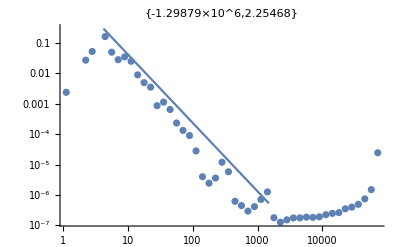
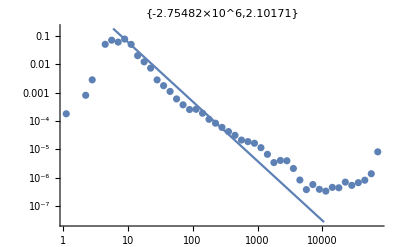
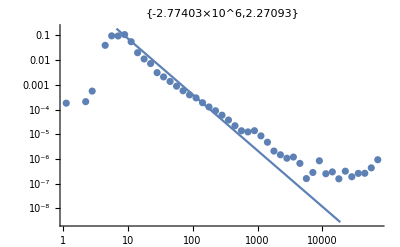
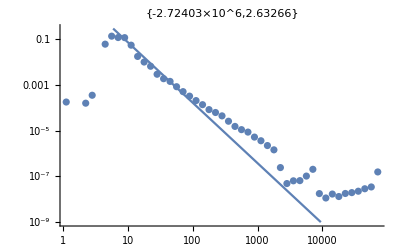
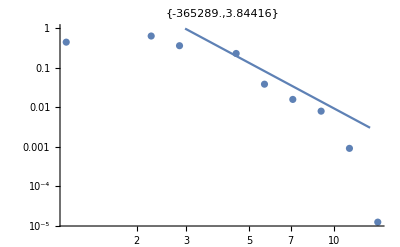
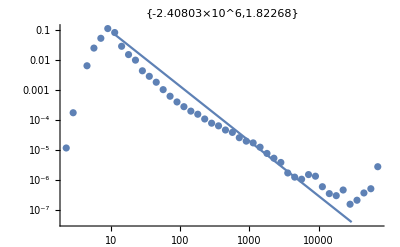
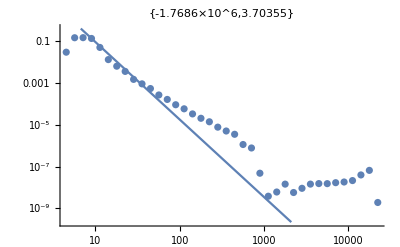
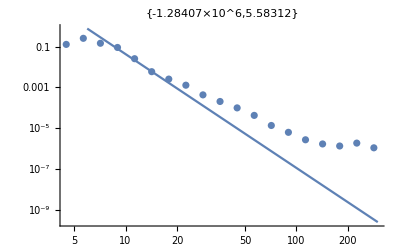

```mathematica
BlockParallel[5,ParallelOuter[{alpha100,g100}↦With[{data=With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},Join@@Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"],{}],{rep,0,999}]]},With[{dataRange=Table[#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],{f,{Max,Min@*Select[Positive]}}]&@HistogramPDFList[data,{"Log",{.05}}]},With[{estDist=EstimatedDistribution[Select[data,Between[dataRange]],TruncatedDistribution[dataRange,ParetoDistribution[α,β]]]},ListLogLogPlot[HistogramPDFList[data,{"Log",{.1}}],PlotLabel->{LogLikelihood[estDist,Select[data,Between[dataRange]]],1+estDist[[2,2]]}]~(Show[##,PlotRange->All]&)~Plot[PDF[estDist,x],{x,Sequence@@dataRange},ScalingFunctions->{"Log","Log"}]]]],{120,200},Range[75,300,75]]]
```

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Grid//Export["fig/relaxationtime_fit_pareto_1000.pdf",#]&
```

fig/relaxationtime_fit_pareto_1000.pdf

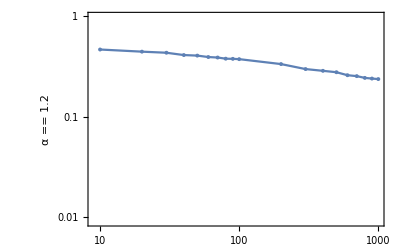
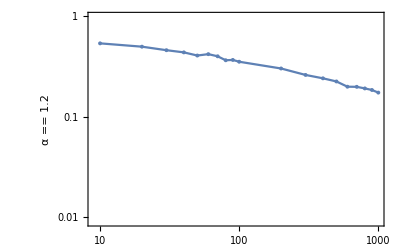
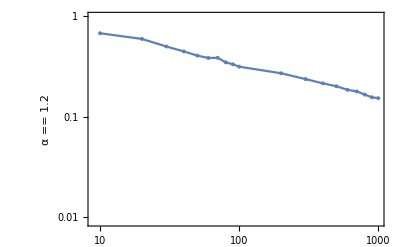
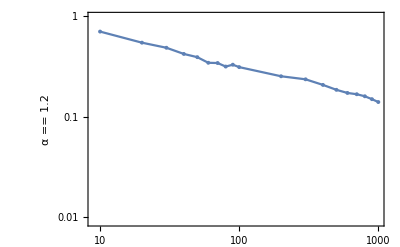
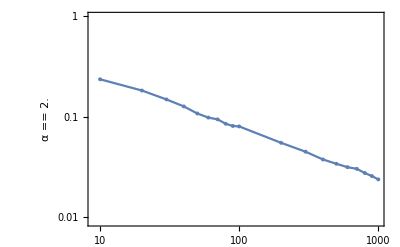
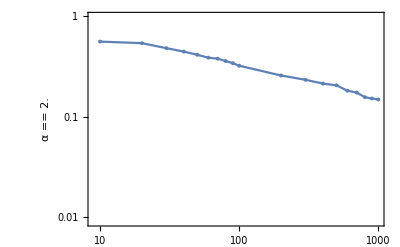
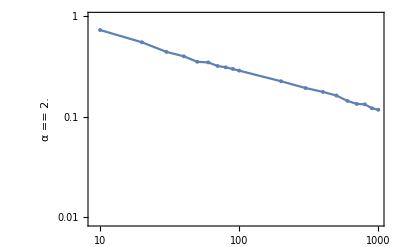
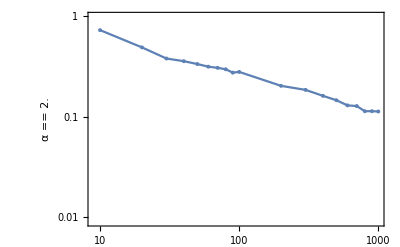

```mathematica
ParallelOuter[{alpha100,g100}↦With[{Ns=Range[10,99,10]~Join~Range[100,1000,100],title="python_ratemodel_scaling_20220626.py_save_scaling_0.001_100000_100_0.25",xticks=Table[{10^n,Superscript[10,n]},{n,1,3,1}],yticks=Table[{10^n,Superscript[10,n]},{n,-2,0,1}]},With[{spreads=Select[NumericQ]/@Table[Quiet@Check[Log@Variance@BinaryReadList[StringTemplate["/import/headnode1/wardak/ext_ander_crit/``/N_``_alpha_``_g_``/rep_``.dat"][title,n,alpha100,g100,rep],"Real32"],Null],{n,Ns},{rep,0,999}]},ListLogLogPlot[Transpose@{Ns,(StandardDeviation@#/Mean@#&)/@spreads},Joined->True(*PlotTheme->"Scientific"*),PlotMarkers->{Automatic,Tiny},Frame->True,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{{StringForm["α == ``",alpha100/100.],},{,StringForm["g == ``",g100/100.]}},Evaluate@FigureStyle@pubStyle[],PlotRangeClipping->False,PlotRange->{{9,1000},{0.009,1}}]]],{120,200},Range[75,300,75]]
```

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//ResourceFunction["PlotGrid"][#,ImageSize->Large,Spacings->20,"ShowFrameLabels"->Automatic]&
```

-Graphics-

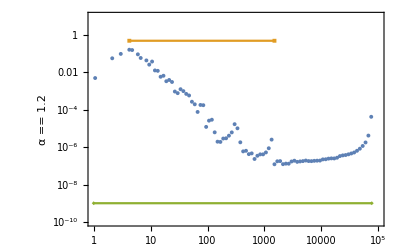
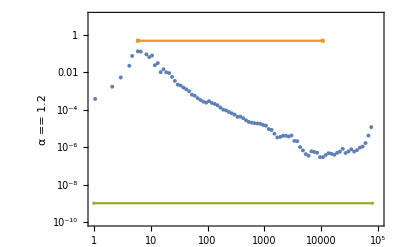
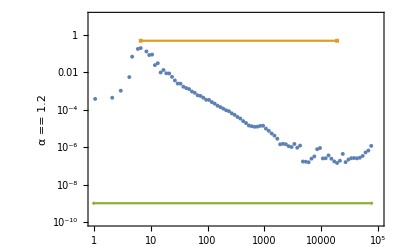
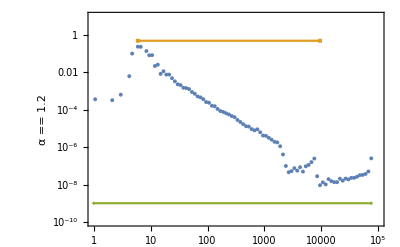
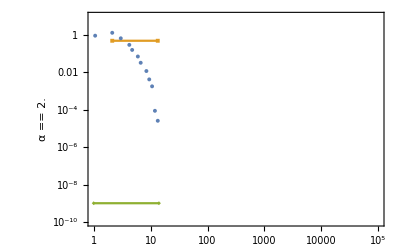
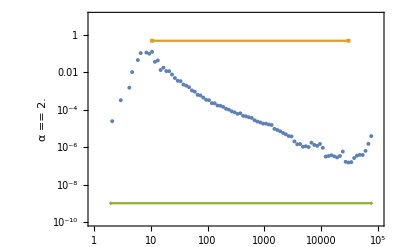
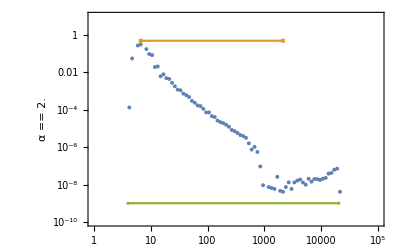
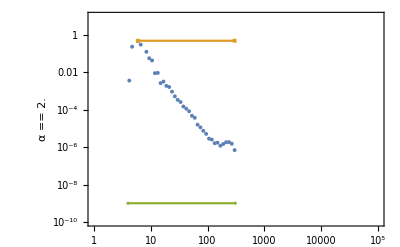

```mathematica
With[{xticks=Table[{10^n,Superscript[10,n]},{n,1,4,1}],yticks=Table[{10^n,Superscript[10,n]},{n,-9,-1,4}]},ParallelOuter[{alpha100,g100}↦With[{data=With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},Join@@Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"],{}],{rep,0,999}]]},ListLogLogPlot[{#,Table[{#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],.5},{f,{Max(*Max PDF*),Min@*Select[Positive](*Min non-zero PDF*)}}],({#,1*^-9}&/@MinMax[data])}&@HistogramPDFList[data,{"Log",{.05}}],PlotRange->{{1,100000},{1*^-10,10}},Joined->{False,True,True}(*PlotTheme->"Scientific"*),PlotMarkers->{Automatic,Tiny},Frame->True,FrameTicks->{{yticks,None},{xticks,None}},FrameLabel->{{StringForm["α == ``",alpha100/100.],},{,StringForm["g == ``",g100/100.]}},Evaluate@FigureStyle@pubStyle[],PlotRangeClipping->False]],{120,200},Range[75,300,75]]]
```

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//ResourceFunction["PlotGrid"][#,ImageSize->Large]&//Export["fig/relaxationtime_0.25_bounds.pdf",#]&
```

fig/relaxationtime_0.25_bounds.pdf

```mathematica
ParallelOuter[{alpha100,g100,rep}↦With[{data=With[{title="ratemodel_20211202_run_subjob_2000_0.1_1000000_10_0.25"},BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"]]},ListLogLogPlot[{(*{{#[[1,1]],1*^-20},Sequence@@#,{#[[-1,1]],1*^-20}}*)#,Table[{#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],.5},{f,{Max,Min@*Select[Positive]}}],({#,1*^-9}&/@MinMax[data])}&@HistogramPDFList[data,{"Log",{.1}}],PlotRange->{{1,100000},{1*^-10,10}},Joined->{False,True,True},PlotMarkers->{Automatic,Tiny},Frame->True,FrameTicks->None]],{120,200},Range[75,300,75],Range[16]]//BinarySerialize
```

ByteArray[…]

```mathematica
BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][]//Grid[Map[ResourceFunction["PlotGrid"]@Partition[#,3]&,#,{2}],Frame->All]&//Export["fig/relaxationtime_0.25_bounds_reps_2000.pdf",#]&
```

fig/relaxationtime_0.25_bounds_reps_2000.pdf

```mathematica
ParallelOuter[{alpha100,g100,rep}↦With[{data=With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"]]},ListLogLogPlot[{(*{{#[[1,1]],1*^-20},Sequence@@#,{#[[-1,1]],1*^-20}}*)#,Table[{#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],.5},{f,{Max,Min@*Select[Positive]}}],({#,1*^-9}&/@MinMax[data])}&@HistogramPDFList[data,{"Log",{.1}}],PlotRange->{{1,100000},{1*^-10,10}},Joined->{False,True,True},PlotMarkers->{Automatic,Tiny},Frame->True,FrameTicks->None]],{120,200},Range[75,300,75],Range[16]]//BinarySerialize
```

ByteArray[…]

```mathematica
BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][]//Grid[Map[ResourceFunction["PlotGrid"]@Partition[#,3]&,#,{2}],Frame->All]&//Export["fig/relaxationtime_0.25_bounds_reps.pdf",#]&
```

fig/relaxationtime_0.25_bounds_reps.pdf

```mathematica
PrintTemporary@Dynamic@{p,g100,rep};Table[With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_"<>p},Apply[Join,Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,120,g100,rep],"Real32"],{}],{g100,75,300,75},{rep,0,999}],{1}]/(1*1)//PlotDistWithLogLogInset[Sequence@@#]&]//Export["fig/relaxationtime_"<>p<>"_alpha_120.pdf",#]&,{p,{"0.25","0.5","0.75"}}]
```

{fig/relaxationtime_0.25_alpha_120.pdf,fig/relaxationtime_0.5_alpha_120.pdf,fig/relaxationtime_0.75_alpha_120.pdf}

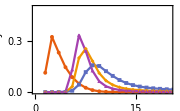

```mathematica
PrintTemporary@Dynamic@{g100,rep};With[{title="ratemodel_20211202_run_subjob_1000_0.1_1000000_10_0.25"},Apply[Join,Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,200,g100,rep],"Real32"],{}],{g100,75,300,75},{rep,0,999}],{1}]/(1*1)//PlotDistWithLogLogInset[Sequence@@#]&]
```

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Export["fig/relaxationtime_0.25_alpha_200_bounds.pdf",#]&
```

fig/relaxationtime_0.25_alpha_200_bounds.pdf

n=2000 (took ~100h on artemis)

find ratemodel_20211202_run_subjob_2000_0.1_1000000_10_0.25/job/ -name *OU | xargs -n1 grep elapsed | tqdm | cut -f1 -d' ' | python -c 'import sys, numpy as np; vals = [float(x) for x in sys.stdin.readlines()]; print(np.mean(vals), np.std(vals), np.min(vals), np.max(vals), len(vals))'
8000it [03:00, 44.33it/s]
8594.920520690024 14894.85086414295 975.4864897727966 57156.72592878342 8000

```mathematica
Run[StringTemplate["rsync mwar3732@hpc.sydney.edu.au:/project/THAP/mwar3732/`` /import/orr1/wardak/artemis -av --exclude='job/*'"]["ratemodel_20211202_run_subjob_2000_0.1_1000000_10_0.25"]]
```

0

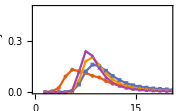

```mathematica
PrintTemporary@Dynamic@{g100,rep};With[{title="ratemodel_20211202_run_subjob_2000_0.1_1000000_10_0.25"},Apply[Join,Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,120,g100,rep],"Real32"],{}],{g100,75,300,75},{rep,0,999}],{1}]/(1*1)//PlotDistWithLogLogInset[Sequence@@#]&]
```

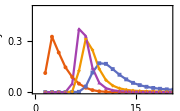

```mathematica
PrintTemporary@Dynamic@{g100,rep};With[{title="ratemodel_20211202_run_subjob_2000_0.1_1000000_10_0.25"},Apply[Join,Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,200,g100,rep],"Real32"],{}],{g100,75,300,75},{rep,0,999}],{1}]/(1*1)//PlotDistWithLogLogInset[Sequence@@#]&]
```

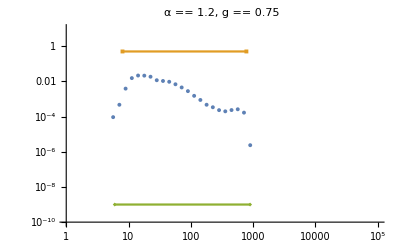
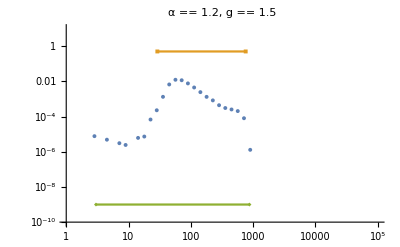
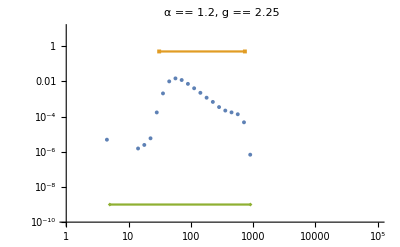
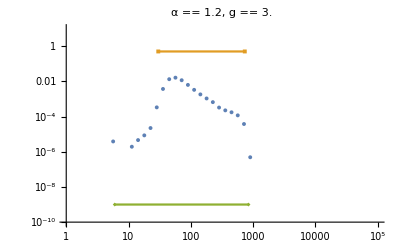
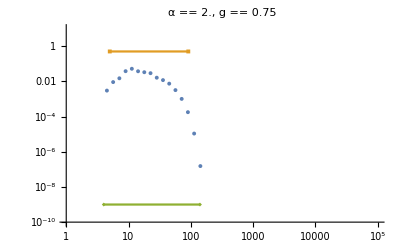
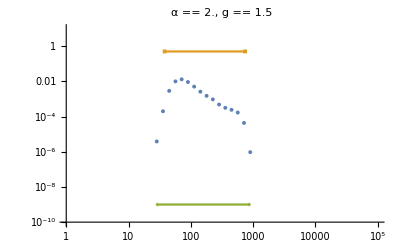
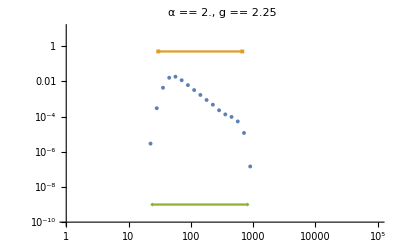
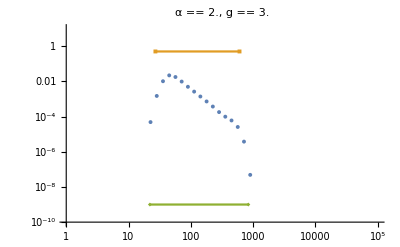

```mathematica
ParallelOuter[{alpha100,g100}↦With[{data=With[{title="ratemodel_20220408_gpu_run_subjob_2000_0.001_100000_100_0.25"},Join@@Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"],{}],{rep,0,99}]]},ListLogLogPlot[{(*{{#[[1,1]],1*^-20},Sequence@@#,{#[[-1,1]],1*^-20}}*)#,{#,.5}&/@Exp@Quantile[Log@data,{.001,.999}],({#,1*^-9}&/@MinMax[data])}&@HistogramPDFList[data,{"Log",{.1}}],PlotRange->{{1,100000},{1*^-10,10}},Joined->{False,True,True}(*PlotTheme->"Scientific"*),PlotMarkers->{Automatic,Tiny},FrameTicks->{Table[{10^n,StringForm["10^(``)",n]},{n,1,5,2}],Table[{10^n,StringForm["10^(``)",n]},{n,-9,-1,4}]},PlotLabel->StringForm["α == ``, g == ``",alpha100/100.,g100/100.]]],{120,200},Range[75,300,75]]
```

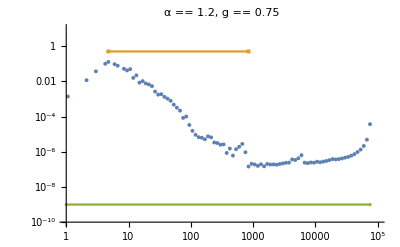
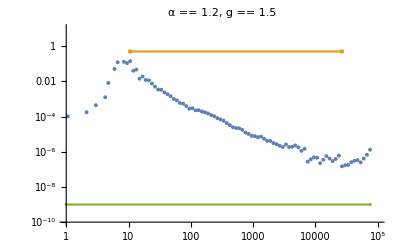
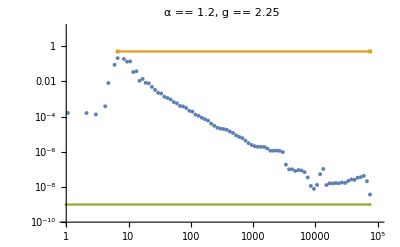
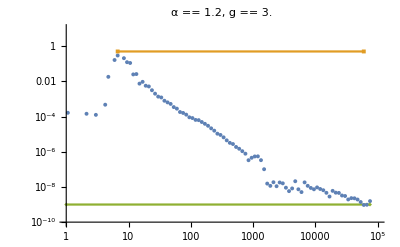
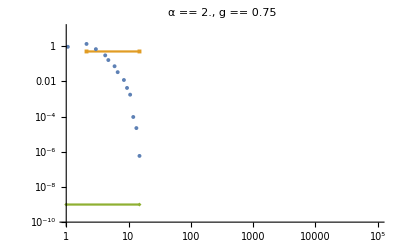
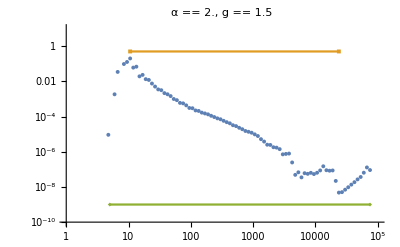
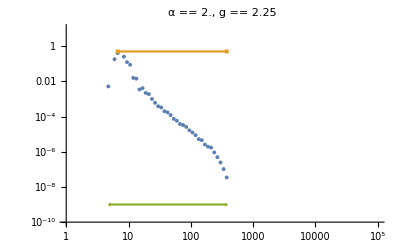
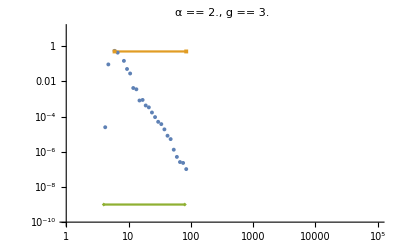

```mathematica
ParallelOuter[{alpha100,g100}↦With[{data=With[{title="ratemodel_20211202_run_subjob_2000_0.1_1000000_10_0.25"},Join@@Table[Quiet@Check[BinaryReadList[StringTemplate["/import/orr1/wardak/artemis/``/alpha_``_g_``_rep_``.dat"][title,alpha100,g100,rep],"Real32"],{}],{rep,0,999}]]},ListLogLogPlot[{(*{{#[[1,1]],1*^-20},Sequence@@#,{#[[-1,1]],1*^-20}}*)#,Table[{#[[First@FirstPosition[#[[;;,2]],f@#[[;;,2]]],1]],.5},{f,{Max,Min@*Select[Positive]}}](*,{#,.5}&/@Exp@Quantile[Log@data,{.01,.99}]*),({#,1*^-9}&/@MinMax[data])}&@HistogramPDFList[data,{"Log",{.05}}],PlotRange->{{1,100000},{1*^-10,10}},Joined->{False,True,True}(*PlotTheme->"Scientific"*),PlotMarkers->{Automatic,Tiny},FrameTicks->{Table[{10^n,StringForm["10^(``)",n]},{n,1,5,2}],Table[{10^n,StringForm["10^(``)",n]},{n,-9,-1,4}]},PlotLabel->StringForm["α == ``, g == ``",alpha100/100.,g100/100.]]],{120,200},Range[75,300,75]]
```

## Reservoir computing task

Network simulations on the cluster (20m on 400 cores for 5 network seeds):

python ratemodel_20220420.py submit_reps_classifier 250 0.01 30000 100 10 1 0.3 1 100 200 20 300 300 1 0 19 0 49 120 defaultQ 1GB

Classification and readout (30m on 30 cores (multithreaded) for 5 network seeds)

python ratemodel_20220420.py submit_reps_readout 250 0.01 30000 100 10 1 0.3 1 0 0 0.8 100 200 20 300 300 1 0 19 0 49 120 defaultQ 15GB

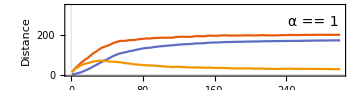
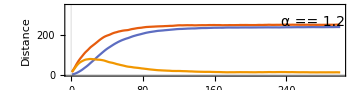
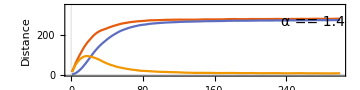
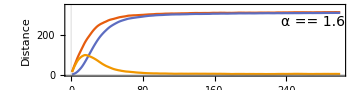
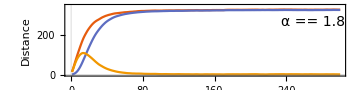
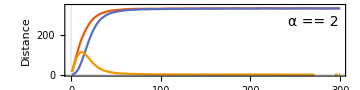

```mathematica
distPlots=Table[(Mean)@Table[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/ratemodel_20220420_run_subjob_classifier_250_0.01_30000_100_10_1_0.3_1/alpha_``_g_300_seed_``_distances.dat"][alpha100,seed],"Real32"]//ArrayReshape[#,{2,300}]&,{seed,0,99}]//{#[[1]],#[[2]],#[[1]]-#[[2]]}&//Show[ListLinePlot[#,FrameLabel->{"Time","Distance"}(*PlotLabel->StringTemplate["α == ``"][alpha100/100]*),LabelStyle->pubStyle[],ImageSize->Medium,PlotRange->{{-1,Full},{0,350}},AspectRatio->1/4,PlotTheme->"Scientific",FrameStyle->pubStyle[],FrameTicks->linearFrameTicks,PlotLegends->If[alpha100==200,Placed[{Subsuperscript["StyleBox[\"H\",FontSlant->\"Italic\"]","12"," s"],Subsuperscript["StyleBox[\"H\",FontSlant->\"Italic\"]","12"," n"],"ΔSubscriptBox[StyleBox[\"H\",FontSlant->\"Italic\"], \"12\"]"},Scaled@{.5,.46}],""]],Graphics@Inset[Style[StringTemplate["α == ``"][alpha100/100],pubStyle[]],{270,270}]]&,{alpha100,100,200,20}]
```

```mathematica
Table[With[{plotData=Table[(Around@@@Transpose@{Mean@#,Quantile[#,{.05,.95}]-Mean@#(*StandardDeviation@#*)}&)@Table[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/ratemodel_20220420_run_subjob_classifier_250_0.01_30000_100_10_1_0.3_1/alpha_``_g_300_seed_``_``_``_0.0.dat"][alpha100,seed,accString,"0.0"],"Real32"],{seed,0,99}],{accString,{"accuracies","accuracies_shuffled"}}]},Table[ListLinePlot[plotData,IntervalMarkers->"Bands",FrameLabel->{{If[yLim==1,"Accuracy"],If[yLim≠1,StringTemplate["α == ``"][alpha100/100.]]},{"Time",}},LabelStyle->pubStyle[],ImageSize->Medium,PlotRange->{{-1,Full},{0,yLim}},AspectRatio->1/4,PlotTheme->"Scientific",FrameStyle->pubStyle[12],FrameTicks->linearFrameTicks],{yLim,{1,.1}}]],{alpha100,Range[100,200,20]}]//BinarySerialize
```

ByteArray[…]

```mathematica
BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][]//ResourceFunction["PlotGrid"][#,Spacings->{40,None},ImageSize->Large]&
```

-Graphics-

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Export["fig/classifier_full.pdf",#]&
```

fig/classifier_full.pdf

```mathematica
Table[With[{plotData=Table[(Around@@@Transpose@{Mean@#,Quantile[#,{.05,.95}]-Mean@#(*StandardDeviation@#*)}&)@Table[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/ratemodel_20220420_run_subjob_classifier_250_0.01_300000_1000_10_1_0.3_1/alpha_``_g_300_seed_``_``_``_0.0.dat"][alpha100,seed,accString,"0.0"],"Real32"],{seed,0,19}],{accString,{"accuracies","accuracies_shuffled"}}]},Table[ListLinePlot[plotData,IntervalMarkers->"Bands",FrameLabel->{{If[yLim==1,"Accuracy"],If[yLim≠1,StringTemplate["α == ``"][alpha100/100.]]},{"Time",}},LabelStyle->pubStyle[],ImageSize->Medium,PlotRange->{{-1,Full},{0,yLim}},AspectRatio->1/4,PlotTheme->"Scientific",FrameStyle->pubStyle[12],FrameTicks->linearFrameTicks,DataRange->{10,3000}],{yLim,{1,.1}}]],{alpha100,Range[100,200,20]}]//BinarySerialize
```

ByteArray[…]

```mathematica
BinaryDeserialize@ResourceFunction["EvaluatePreviousCell"][]//ResourceFunction["PlotGrid"][#,Spacings->{40,None},ImageSize->Large]&
```

-Graphics-

```mathematica
ResourceFunction["EvaluatePreviousCell"][]//Export["fig/classifier_full_long.pdf",#]&
```

fig/classifier_full_long.pdf

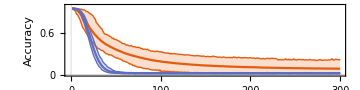

```mathematica
accPlot=Table[(Around@@@Transpose@{Mean@#,Quantile[#,{.05,.95}]-Mean@#(*StandardDeviation@#*)}&)@Table[BinaryReadList[StringTemplate["/import/headnode1/wardak/Desktop/ratemodel_20220420_run_subjob_classifier_250_0.01_30000_100_10_1_0.3_1/alpha_``_g_300_seed_``_accuracies_``_0.0.dat"][alpha100,seed,"0.0"],"Real32"],{seed,0,99}],{alpha100,{100,200}}]//ListLinePlot[#,IntervalMarkers->"Bands",FrameLabel->{"Time","Accuracy"},LabelStyle->pubStyle[],ImageSize->Medium,PlotRange->{{-1,Full},{0,1}},AspectRatio->1/4,PlotTheme->"Scientific",FrameStyle->pubStyle[],FrameTicks->linearFrameTicks,PlotLegends->Placed[StringTemplate["α == ``"]/@({100,200}/100),Scaled@{.8,.6}]]&
```

```mathematica
{{distPlots[[1]]},{distPlots[[-1]]},{accPlot}}//ResourceFunction["PlotGrid"]
```

-Graphics-

```mathematica
ResourceFunction["EvaluatePreviousCell"][]/.{Unevaluated->Identity}//Export["fig/classifier.pdf",#]&
```

fig/classifier.pdf